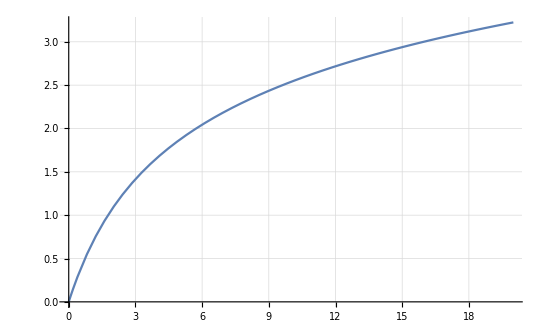

```mathematica
Plot[{-Log[Erfc[x/Sqrt[2]]]-(x^2/2+0x/3)},{x,0,20},GridLines->Automatic]
```

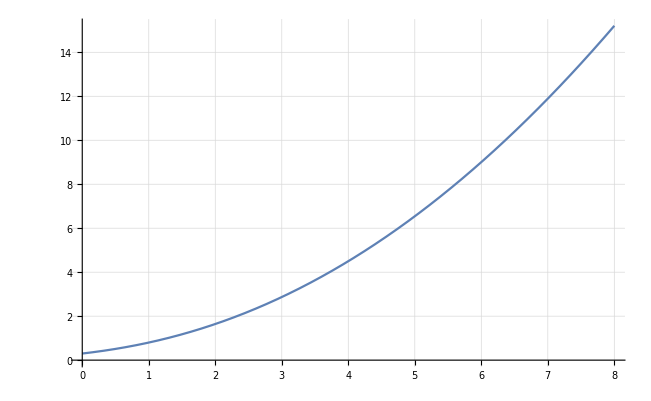

```mathematica
Plot[-Log10[1/2Erfc[x/Sqrt[2]]],{x,0,8},GridLines->Automatic]
```

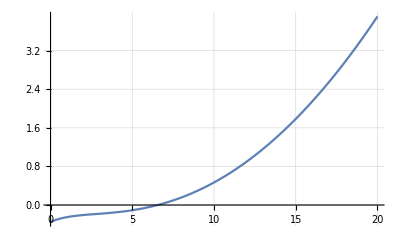

```mathematica
Plot[{-Log10[Erfc[x/Sqrt[2]]]-((x+.5)^2/5+.3)},{x,0,20},GridLines->Automatic]
```

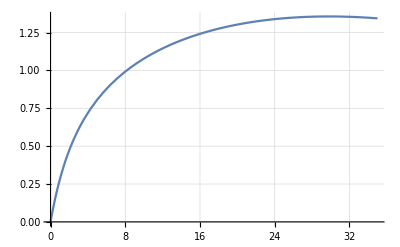

```mathematica
Plot[{-Log10[Erfc[x/Sqrt[2]]]-(x^2/4.6)},{x,0,35},GridLines->Automatic]
```

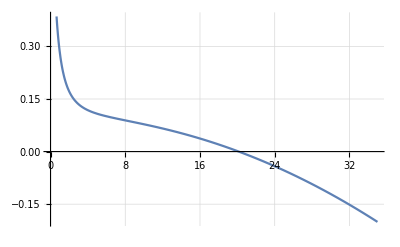

```mathematica
Plot[{-Log10[Erfc[x/Sqrt[2]]]-(x^2/4.6)-Log10[x]},{x,0,35},GridLines->Automatic]
```

```mathematica
Series[-Log10[Erfc[x/Sqrt[2]]],{x,Infinity,2}]
```

-Log[ⅇ^(-x^2/2+O[1/x]^3) ((√(2/π))/x+O[1/x]^3)]/Log[10]

```mathematica
3.5^2/5+.3
```

2.75

```mathematica
10^-(8.5^2/5+.3)
```

1.77828×10^-15

```mathematica
Erfc[8./Sqrt[2]]
```

1.24419×10^-15

```mathematica
dat=Table[{x,-Log10[Erfc[x/Sqrt[2]]]},{x,3.1,8,.1}];
```

```mathematica
?Fit
```

```mathematica
Fit[dat,{1,n,n^2},{n}]
```

2.57433+0.141148 n+0.00210806 n^2

```mathematica
fit=NonlinearModelFit[dat,{(x+.5)^2/5+x/c},{b,c},{x}]
```

FittedModel[0.0457996 x+1/5 (0.5+x)^2]

```mathematica
fit["BestFit"]/.{n->10(x-3)}//Simplify
```

0.204857 (0.523308+x)^2

```mathematica
Factor[0.23713798393653174+0.14664460652636646 x+0.21080641746869383 x^2]
```

0.210806 (1.12491+0.695636 x+1. x^2)

```mathematica
CDF[NormalDistribution[]][-x]
```

1/2 Erfc[x/(√2)]

```mathematica
1/2Erfc[-Sqrt[2]]//N
```

0.97725

```mathematica
NumberForm[0.9772498680518208,16]
```

0.977249868051821

```mathematica
Log10[CDF[NormalDistribution[]][-3.]]
-3^2/%
InverseCDF[NormalDistribution[],1./(8*^9)]
Log10[CDF[NormalDistribution[]][-6.33]]
-6.33^2/%
```

-2.8697

3.13622

-6.32698

-9.91158

4.04264

```mathematica
5.6^2/3.2
```

9.8